## data

```mathematica
Clear["Global`*"]
Needs["ErrorBarLogPlots`"]
survival={{{-30.,0.058394160583941604},ErrorBar[{-0.017015721366339796,0.023415805995558037}]},{{-27.,0.046511627906976744},ErrorBar[{-0.015308156342208019,0.022284900528254534}]},{{-24.,0.07086614173228346},ErrorBar[{-0.019574390249562576,0.026279606784995663}]},{{-21.,0.03759398496240601},ErrorBar[{-0.013339474289574028,0.02024105660356796}]},{{-18.,0.07462686567164178},ErrorBar[{-0.01968473415956476,0.02598655837183675}]},{{-15.,0.11475409836065574},ErrorBar[{-0.02577655275612928,0.032040713758395026}]},{{-12.,0.14685314685314685},ErrorBar[{-0.027145986586342527,0.03205080399115992}]},{{-9.,0.18518518518518517},ErrorBar[{-0.031074639575576435,0.035704269205206085}]},{{-6.,0.21818181818181817},ErrorBar[{-0.03674454666082047,0.04182235173862556}]},{{-3.,0.42016806722689076},ErrorBar[{-0.04439765027987186,0.04572818249275701}]},{{0.,0.5737704918032787},ErrorBar[{-0.04519387899221161,0.04399435880028846}]},{{3.,0.546875},ErrorBar[{-0.04419353828642891,0.043466794100382344}]},{{6.,0.27419354838709675},ErrorBar[{-0.03813544166607988,0.041748344891886335}]},{{9.,0.20512820512820512},ErrorBar[{-0.03475735472056379,0.03975518175228915}]},{{12.,0.25862068965517243},ErrorBar[{-0.038471182840801116,0.04259732489797763}]},{{15.,0.20833333333333334},ErrorBar[{-0.03458781272331485,0.0394087493624333}]},{{18.,0.14615384615384616},ErrorBar[{-0.028281356441389932,0.03368358779781974}]},{{21.,0.14285714285714285},ErrorBar[{-0.028365942748110662,0.03399023971099033}]},{{27.,0.04477611940298507},ErrorBar[{-0.014744108228602629,0.021488165718928774}]},{{30.,0.08527131782945736},ErrorBar[{-0.021511569428196098,0.02789201069235832}]},{{135.,0.06504065040650407},ErrorBar[{-0.01891346710437914,0.025928940484919394}]},{{138.,0.047619047619047616},ErrorBar[{-0.015667777649732387,0.022791887136046587}]},{{141.,0.11475409836065574},ErrorBar[{-0.02577655275612928,0.032040713758395026}]},{{144.,0.1},ErrorBar[{-0.024166562212553158,0.03077813246048705}]},{{147.,0.10638297872340426},ErrorBar[{-0.023250348304902996,0.02879425001302406}]},{{150.,0.08620689655172414},ErrorBar[{-0.022651110910026334,0.029724497293757535}]},{{153.,0.171875},ErrorBar[{-0.03077056867765715,0.03585777797998271}]},{{156.,0.19642857142857142},ErrorBar[{-0.03478445091094545,0.04015739654937783}]},{{159.,0.203125},ErrorBar[{-0.03319604473646165,0.037798757914756204}]},{{162.,0.23140495867768596},ErrorBar[{-0.03604351695049815,0.04044671434922459}]},{{165.,0.216},ErrorBar[{-0.03447586121595847,0.03898379772389496}]},{{168.,0.28},ErrorBar[{-0.038292057954379205,0.04178412144644261}]},{{171.,0.3082706766917293},ErrorBar[{-0.03848646765320157,0.04134809934436984}]},{{174.,0.31092436974789917},ErrorBar[{-0.04070796776254809,0.04385922826674976}]},{{177.,0.1721311475409836},ErrorBar[{-0.03147613939278465,0.03680734024577678}]},{{180.,0.08148148148148149},ErrorBar[{-0.020582342931440872,0.026737027027301435}]},{{183.,0.09836065573770492},ErrorBar[{-0.023784327932772034,0.030315048977687414}]},{{186.,0.04316546762589928},ErrorBar[{-0.01422013480919318,0.02074634241453748}]},{{189.,0.08527131782945736},ErrorBar[{-0.021511569428196098,0.02789201069235832}]},{{192.,0.04672897196261682},ErrorBar[{-0.016541213742885762,0.024935121669503964}]},{{195.,0.02608695652173913},ErrorBar[{-0.011267454030294138,0.019438368573022783}]},{{240.,0.06896551724137931},ErrorBar[{-0.020030275357781485,0.027398386174168163}]}};
```

```mathematica
survival2={{{-125.,0.034482758620689655},ErrorBar[{-0.014867443021315957,0.025447380325391192}]},{{-105.,0.056818181818181816},ErrorBar[{-0.02005899058581262,0.03001813256742652}]},{{-102.,0.08333333333333333},ErrorBar[{-0.024094006257488483,0.03268507154958472}]},{{-99.,0.022222222222222223},ErrorBar[{-0.011069599079325131,0.02157020957993563}]},{{-96.,0.03225806451612903},ErrorBar[{-0.013914792924695763,0.023866748998820686}]},{{-93.,0.0375},ErrorBar[{-0.01615801183199797,0.027577764918417715}]},{{-90.,0.0379746835443038},ErrorBar[{-0.016360895214068062,0.02791152812546046}]},{{-87.,0.07608695652173914},ErrorBar[{-0.023310537891891157,0.03242694742905805}]},{{-84.,0.15217391304347827},ErrorBar[{-0.03369344629643746,0.041173577198728245}]},{{-81.,0.22666666666666666},ErrorBar[{-0.044563320832314735,0.051756303288455124}]},{{-78.,0.35555555555555557},ErrorBar[{-0.04861723384166372,0.051791837016266884}]},{{-75.,0.5176470588235295},ErrorBar[{-0.054088384075767826,0.05367798735894147}]},{{-72.,0.44086021505376344},ErrorBar[{-0.05058376867683817,0.05184206197356661}]},{{-69.,0.2},ErrorBar[{-0.042105263157894736,0.05}]},{{-66.,0.09876543209876543},ErrorBar[{-0.02841515717541003,0.03820136614861086}]},{{-63.,0.1276595744680851},ErrorBar[{-0.030542192034689372,0.038380937835361284}]},{{-60.,0.1527777777777778},ErrorBar[{-0.03761958415510791,0.047132521750237216}]},{{-57.,0.0963855421686747},ErrorBar[{-0.02775174005617588,0.03736160809977887}]},{{-54.,0.07142857142857142},ErrorBar[{-0.023343438242108452,0.03342747185555385}]},{{-51.,0.03896103896103896},ErrorBar[{-0.016782337234845415,0.028603849056357253}]},{{-48.,0.07954545454545454},ErrorBar[{-0.024344538131391986,0.033792954883179516}]},{{-45.,0.061855670103092786},ErrorBar[{-0.020270336309323803,0.02921205732762802}]},{{70.,0.022222222222222223},ErrorBar[{-0.011069599079325131,0.02157020957993563}]},{{73.,0.07865168539325842},ErrorBar[{-0.02407754426137436,0.03344084014152418}]},{{76.,0.06976744186046512},ErrorBar[{-0.022811444429014248,0.03270184806440586}]},{{79.,0.05102040816326531},ErrorBar[{-0.01803987114618308,0.02711016593076357}]},{{82.,0.09278350515463918},ErrorBar[{-0.02544527103413141,0.03375581174526121}]},{{85.,0.15730337078651685},ErrorBar[{-0.03475878518650943,0.04237426583569798}]},{{88.,0.10465116279069768},ErrorBar[{-0.02858661507710404,0.03767509409340984}]},{{91.,0.11627906976744186},ErrorBar[{-0.030238838075648672,0.03906000888559254}]},{{94.,0.10869565217391304},ErrorBar[{-0.02834137201356865,0.0367565192786458}]},{{97.,0.09},ErrorBar[{-0.024704631774918703,0.03282344365610683}]},{{100.,0.14444444444444443},ErrorBar[{-0.03315073631794209,0.04096514413234992}]},{{103.,0.09411764705882353},ErrorBar[{-0.027118527895691066,0.03655765238269518}]},{{106.,0.010101010101010102},ErrorBar[{-0.006236085268690784,0.01603406506667058}]},{{109.,0.034482758620689655},ErrorBar[{-0.014867443021315957,0.025447380325391192}]},{{112.,0.05747126436781609},ErrorBar[{-0.020286027882979153,0.030343499147346978}]},{{115.,0.06818181818181818},ErrorBar[{-0.02230313593066075,0.03200691529736148}]},{{118.,0.043010752688172046},ErrorBar[{-0.01662133996294797,0.02634451543766772}]},{{121.,0.06521739130434782},ErrorBar[{-0.021351523151965424,0.030701686779828916}]},{{124.,0.021739130434782608},ErrorBar[{-0.010829846008280982,0.021115025998930816}]},{{127.,0.05319148936170213},ErrorBar[{-0.018796720229108457,0.02820321518991472}]},{{130.,0.030927835051546393},ErrorBar[{-0.013344730857503883,0.02291763218298252}]},{{150.,0.03333333333333333},ErrorBar[{-0.014375354596299097,0.024631764852709355}]}};
```

## plot

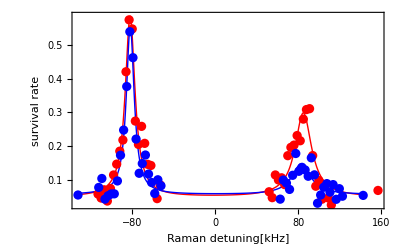

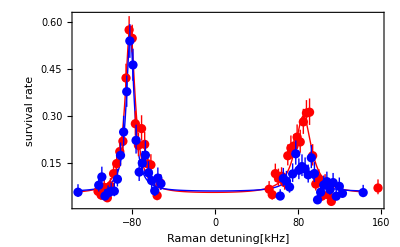

```mathematica
globalShift=-83;
x1=survival[[;;,1,1]]+globalShift;
y1=survival[[;;,1,2]];
err1=survival[[;;,2]];
survival1=Thread[{Thread[{x1,y1}],err1}];

x2=survival2[[;;,1,1]]+globalShift+75.7;
y2=survival2[[;;,1,2]]+.021;
err2=survival2[[;;,2]];
survivalShifted=Thread[{Thread[{x2,y2}],err2}];

fits=Reap[
Do[
lorentzian2=offs+(A (1/2 Γ)^2)/((f-f0)^2+(1/2 Γ)^2)+(A2 (1/2 Γ2)^2)/((f-f02)^2+(1/2 Γ2)^2);
{offs0,A0,f00,Γ0,A200,f020,Γ20}={0.4,.6,+globalShift,10,.1,165+globalShift,20};
data={survival1,survivalShifted}[[i]];
nlm=NonlinearModelFit[data[[;;,1]],lorentzian2,{{offs,offs0},{ A,A0}, {f0,f00}, {Γ,Γ0},{ A2,A200}, {f02,f020}, {Γ2,Γ20}},f(*,Weights->weights*)];

fit=nlm["BestFitParameters"];

Sow[fit]

,{i,2}
]
][[2,1]];
fit1=lorentzian2/.fits[[1]];
fit2=lorentzian2/.fits[[2]];
Show[
{Plot[{fit1,fit2},{f,data[[1,1,1]],data[[-1,1,1]]},PlotRange->All,PlotStyle->{{Thin,Red},{Thin,Blue}},
Axes->False,Frame->True,FrameLabel->{"Raman detuning[kHz]","survival rate"}],
ListPlot[{survival1[[;;,1]],survivalShifted[[;;,1]]},PlotStyle->{{Thin,Red},{Thin,Blue}}]
}]

Show[
{Plot[{fit1,fit2},{f,data[[1,1,1]],data[[-1,1,1]]},PlotRange->All,PlotStyle->{{Thin,Red},{Thin,Blue}},
Axes->False,Frame->True,FrameLabel->{"Raman detuning[kHz]","survival rate"}],
ErrorListPlot[{survival1,survivalShifted},PlotStyle->{{Thin,Red},{Thin,Blue}}]
}]
```